```mathematica
seqList100 = {{1,1},{2,1.44/1.31},{3,1.42/1.31},{4,1.22/1.31},{6,1.24/1.31},{8,.994/1.31},{10,1.09/1.31},{12,0.984/1.31},{16,.8376/1.31},{32,.5378/1.31},{64,.2950/1.31},{128,.1430/1.31}};
threadList100 ={{1,1},{2,1.44/1.27},{3,1.42/1.27},{4,1.22/1.27},{6,1.24/1.27},{8,.994/1.27},{10,1.09/1.27},{12,0.984/1.27},{16,.8376/1.27},{32,.5378/1.27},{64,.2950/1.27},{128,.1430/1.27}};
```

```mathematica
seqList1000 = {{1,1},{2,1.51/.7222},{3,2.13/.7222},{4,2.75/.7222},{6,3.63/.7222},{8,4.81/.7222},{10,3.36/.7222},{12,3.82/.7222},{16,4.47/.7222},{32,4.20/.7222},{64,3.56/.7222},{128,2.50/.7222}};
threadList1000 ={{1,1},{2,1.51/.7162},{3,2.13/.7162},{4,2.75/.7162},{6,3.63/.7162},{8,4.81/.7162},{10,3.36/.7162},{12,3.82/.7162},{16,4.47/.7162},{32,4.20/.7162},{64,3.56/.7162},{128,2.50/.7162}};
```

```mathematica
seqList5000 = {{1,1},{2,2.00/1.0745},{3,3.03/1.0745},{4,3.96/1.0745},{6,5.66/1.0745},{8,6.87/1.0745},{10,5.47/1.0745},{12,6.15/1.0745},{16,5.89/1.0745},{32,6.01/1.0745},{64,6.77/1.0745},{128,6.16/1.0745}};
threadList5000 ={{1,1},{2,2.00/.9907},{3,3.03/.9907},{4,3.96/.9907},{6,5.66/.9907},{8,6.87/.9907},{10,5.47/.9907},{12,6.15/.9907},{16,5.89/.9907},{32,6.01/.9907},{64,6.77/.9907},{128,6.16/.9907}};
```

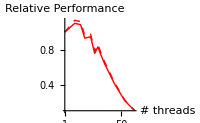

```mathematica
ListLogLinearPlot[{seqList100,threadList100},Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# threads","Relative Performance"},ImageSize->200]
```

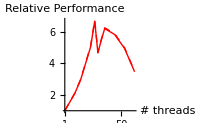

```mathematica
ListLogLinearPlot[{seqList1000,threadList1000},AxesOrigin->Automatic,Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# threads","Relative Performance"},ImageSize->200]
```

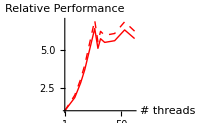

```mathematica
ListLogLinearPlot[{seqList5000,threadList5000},AxesOrigin->Automatic,Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# threads","Relative Performance"},ImageSize->200]
```